```mathematica
l1[p_]:=0.38/0.13*Likelihood[BinomialDistribution[100,p],{10}]
l2[p_]:=Likelihood[BinomialDistribution[10,p],{1}]
```

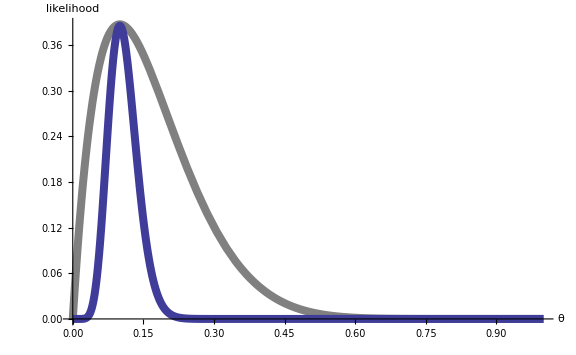

```mathematica
Show[Plot[l2[p],{p,0,1},PlotRange->{Automatic,Full},PlotStyle->{Gray,Thickness[0.01]},AxesLabel->{θ,likelihood},BaseStyle->{FontSize->16}],Plot[l1[p],{p,0,1},PlotRange->{Automatic,Full},PlotStyle->{Thickness[0.01]}],ImageSize->Large]
```